h = 0.05,  x ∈ [1., 1.5] 
{y' (x) =(x^2 (y(x))^2 -  (2 x + 1) y(x) + 1.)/x, 
{y (1.) = 0.)
 Контрольные вопросы : 2, 5, 9

```mathematica
ClearAll["y*"]
rt=NDSolve[{y'[x]==(x^2 y[x]^2-(2 x+1) y[x]+1.)/x,y[1.]==0.},y,{x,1.,1.5}]
yt[x_]:=y[x]/.rt[[1]];
```

{{y→InterpolatingFunction[{{1., 1.5}}, <>]}}

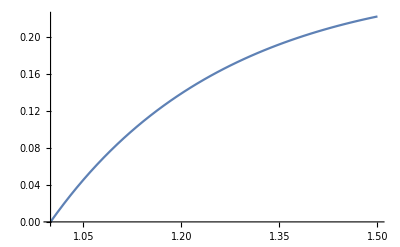

```mathematica
g1=Plot[yt[x],{x,1.,1.5}]
```

```mathematica
f[x_,y_]:=(x^2 y^2-(2 x+1) y+1.)/x;
```

```mathematica
h=0.1;
a=1.;
b=1.5;
x0=a;
y0=0.;
X={x0};
yE={y0};
While[x0<b,x1=x0+h;
(*Вычисление значения решения в точке x1*)  y1 = y0 + h f[x0,y0]; Print[" x= ",x1,"      y= ",y1];
AppendTo[X,x1];(*Добавление узла сетки*)
AppendTo[yE,y1];(*Добавление значения решения в этом узле*)
x0=x1;
y0=y1;
];
```

x= 1.1      y= 0.1

x= 1.2      y= 0.162918

x= 1.3      y= 0.203276

x= 1.4      y= 0.229279

x= 1.5      y= 0.245835

{{1.,0.},{1.1,0.1},{1.2,0.162918},{1.3,0.203276},{1.4,0.229279},{1.5,0.245835}}

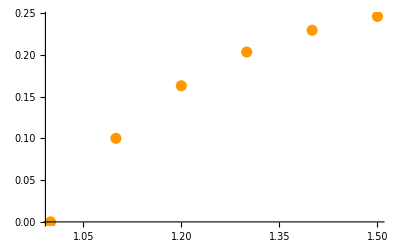

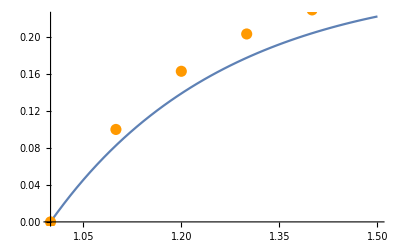

```mathematica
ynum=Transpose[{X,yE}]
g2=ListPlot[ynum,PlotStyle->{Hue[0.1],PointSize[0.02]}]
Show[g1,g2]
```

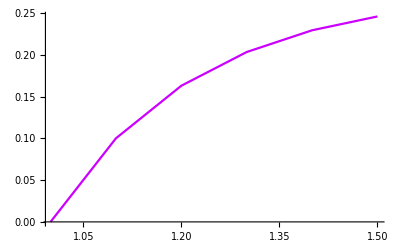

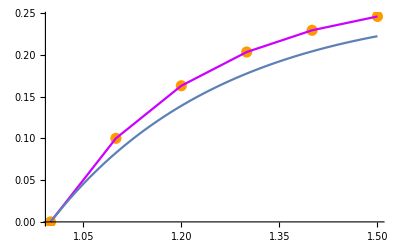

```mathematica
g3=ListPlot[ynum,Joined->True,PlotStyle->{Hue[0.8],PointSize[0.02]}] (*Ломанная Эйлера*)
Show[g2,g3,g1]
```

-Graphics-

```mathematica
f[x_,y_] := (x^2 y^2-(2 x+1) y+1.)/x;
```

```mathematica
h=0.1;
a=1.;
b=1.5;
x0=a;
y0=0.;
X=List[x0];
yR=List[y0];
While[x0<b,x1=x0+h;
 k1=h f[ x0 , y0 ];
     k2=h f[ x0+ h/3 , y0+ k1/3 ];  
k3 = h f[x0 + 2/3 h, y0 + 2/3 k2];
     y1 = y0 +k1/4 + 3/4 k3;Print[" x= ",x1,"     y= ",y1];
AppendTo[X,x1];
AppendTo[yR,y1];
x0=x1;
y0=y1;
];
```

x= 1.1     y= 0.082804

x= 1.2     y= 0.139099

x= 1.3     y= 0.177731

x= 1.4     y= 0.204285

x= 1.5     y= 0.222406

{{1.,0.},{1.1,0.082804},{1.2,0.139099},{1.3,0.177731},{1.4,0.204285},{1.5,0.222406}}

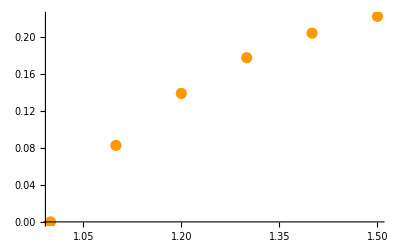

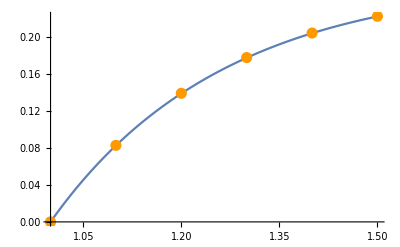

```mathematica
ynum=Transpose[{X,yR}]
g2=ListPlot[ynum,PlotStyle->{Hue[0.1],PointSize[0.02]}]
Show[g1,g2]
```

```mathematica
h=0.1;

b=1.5;
x0=1.;
y0=0.;
n=(b-x0)/h+1;
xA=Table [t,{t,x0,b,h}];
yA=Table[0,{n}] ;
yA[[1]]=yR[[1]];
yA[[2]]=yR[[2]];
yA[[3]]=yR[[3]];
fA = Table[0, {n}];
For[i=3, i<n, i++,
AppendTo[ fA, f[ xA[[i-2]],yA[[i-2]] ]];
AppendTo[fA, f[ xA[[i-1]],yA[[i-1]] ]];
AppendTo[fA, f[ xA[[i]],yA[[i]] ]];
yA[[i+1]]= yA[[i]] + h/12*(23. * fA[i] - 16. * fA[i-1] + 5. * fA[i-2]);
AppendTo[fA, f[ xA[[i+1]],yA[[i+1]] ]];
yA[[i+1]]= yA[[i]] + h/12*(5 * fA[ i+1] + 8 * fA[i ] - f[ i-1 ]);  


]
```

```mathematica
ynumAdams=Table[{xA[[i]],yA[[i]]},{i,n}]
```

{{1.,0.},4,{1.5,0.139099+21 1+1+0.00833333 (-f[4]+8 1+5 {0,0,14,1,0.666667 (1.-4. (20+2+1)+2.25 (1)^2)}[6])}}
 |  |  |  |

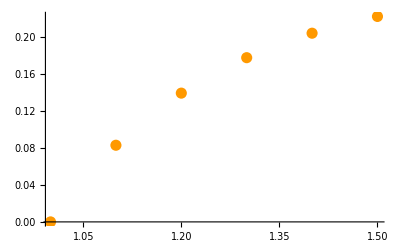

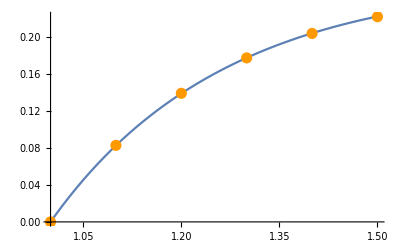

```mathematica
g2Adams=ListPlot[ynumAdams , PlotStyle->{Hue[0.1] , PointSize[0.02]} ] 
Show[g1,g2Adams]
```